RM Universal model
Mathematica’s numerical solver is slightly better than MATLAB’s at the limits of the parameters.
As I am trying to solve for min/max on limit cycles on grid-searched parameter combinations, 
there is a point the ODE gets too stiff; plus, of course this can shoot off to infinity when values
get very close to zero. Hence, there is a small part of the solution space where this does not 
 converge; these values are manually corrected or deleted.
 
You will likely need to correct the directory to run this code.
Assign/define variables

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
mu = 5;
gamma=0.85;
omega =0.5623;
u0 = Log[1.798];
v0 = Log[2.6734];
```

Set up the ODE solution, check if it is behaving

```mathematica
sol = NDSolve[{u'[t] == (1-(Exp[u[t]]/mu)) - gamma*Exp[v[t]]/(1+Exp[u[t]]), 
v'[t] ==  gamma*Exp[u[t]]/(1+Exp[u[t]]) - omega, u[0] == u0, v[0] == v0}, {u,v}, {t,0,1000} ,Method -> "StiffnessSwitching"]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

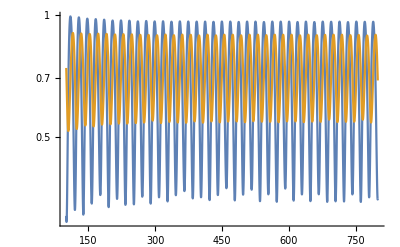

```mathematica
LogPlot[Evaluate[{u[t], v[t]} /. %], {t,100,800}, PlotRange->All, PlotPoints->200]
```

Create vector of different values of mu and gamma to pass to the solution

```mathematica
muvec = Range[5,30,0.5];
gammavec=Range[0.57,0.9,(0.9-0.57)/50];
```

Create functions to get the peak and trough values for the predator and prey

```mathematica
cyclepeakprey[mux_,gammax_,omegax_]:=First@Maximize[{u[t]/.First@NDSolve[{u'[t] == (1-(Exp[u[t]]/mux)) - gammax*Exp[v[t]]/(1+Exp[u[t]]), 
v'[t] ==  gammax*Exp[u[t]]/(1+Exp[u[t]]) - omegax, u[0] == u0, v[0] == v0}, {u,v}, {t,0,1000} ,Method -> "StiffnessSwitching"], 200≤t≤500},{t}]
```

```mathematica
cycletroughprey[mux_,gammax_,omegax_]:=First@Minimize[{u[t]/.First@NDSolve[{u'[t] == (1-(Exp[u[t]]/mux)) - gammax*Exp[v[t]]/(1+Exp[u[t]]), 
v'[t] ==  gammax*Exp[u[t]]/(1+Exp[u[t]]) - omegax, u[0] == u0, v[0] == v0}, {u,v}, {t,0,1000} ,Method -> "StiffnessSwitching"], 200≤t≤500},{t}]
```

```mathematica
cyclepeakpred[mux_,gammax_,omegax_]:=First@Maximize[{v[t]/.First@NDSolve[{u'[t] == (1-(Exp[u[t]]/mux)) - gammax*Exp[v[t]]/(1+Exp[u[t]]), 
v'[t] ==  gammax*Exp[u[t]]/(1+Exp[u[t]]) - omegax, u[0] == u0, v[0] == v0}, {u,v}, {t,0,1000} ,Method -> "StiffnessSwitching"], 200≤t≤500},{t}]
```

```mathematica
cycletroughpred[mux_,gammax_,omegax_]:=First@Minimize[{v[t]/.First@NDSolve[{u'[t] == (1-(Exp[u[t]]/mux)) - gammax*Exp[v[t]]/(1+Exp[u[t]]), 
v'[t] ==  gammax*Exp[u[t]]/(1+Exp[u[t]]) - omegax, u[0] == u0, v[0] == v0}, {u,v}, {t,0,1000} ,Method -> "StiffnessSwitching"], 200≤t≤500},{t}]
```

Create a grid table of values for the different combinations of mu and gamma. Note that at certain limits this won’t converge, however this is easily seen on the plot.

```mathematica
outputtest = Table[cyclepeakpred[i,j,omega]-cycletroughpred[i,j,omega],{i,muvec}, {j,gammavec}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

Take a quick look at the heatmap

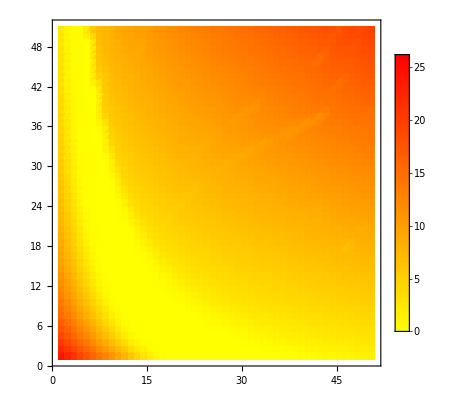

```mathematica
ListDensityPlot[outputtest,PlotLegends->Automatic,ColorFunction->(Blend[{Yellow,Red},#]&)]
```

Export results to use in MATLAB

```mathematica
(*Export["./testheatmap.mat",outputtest]
Export["./muvec.mat",muvec]
Export["./gammavec.mat",gammavec]*)
```

./testheatmap.mat

./muvec.mat

./gammavec.mat